# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
```

# Parameters

```mathematica
nmax=171;
var={u,v,w,z};
par={a,b};
nvar=Length[var];
fixedpar={α->1,β->1/2,δ->(21+√313)/48}//N;
parval={a->3,b->(841+37*√313)/128}//N;
ηval={ηNF->-1843/79830409516*279127306^(1/2)*(4284237-222538*313^(1/2))^(1/2)+(31/39915204758)*87366846778^(1/2)*(4284237-222538*313^(1/2))^(1/2)}//N;
ξval={ξNF->-1/626*87366846778^(1/2)/(4284237-222538*313^(1/2))^(1/2)}//N;
κval={κNF^2->ⅈ}//N;
C11eval={C11->(12/139563653)*279127306^(3/4)*3^(1/2)*I*(1340966181-69654394*313^(1/2))^(1/4)*Exp[-1/626*87366846778^(1/2)*Pi/(4284237-222538*313^(1/2))^(1/2)]/(-313+51*313^(1/2))^(1/2)}//N;
A3eval={Subscript[ANF, 3]->(1/340346519633148728067208840400)*3^(1/2)*(-318817756655985794796789029571746358*87366846778^(3/4)*(4284237-222538*313^(1/2))^(1/2)-908083983851123161417948634774777736974050*279127306^(1/4)*313^(3/4)*Pi+16110767124258199540897793614121861828840950*87366846778^(1/4)*Pi+5637680295594650199764432265704603922*279127306^(3/4)*313^(1/4)*(4284237-222538*313^(1/2))^(1/2)-44348291393081915994301144203437957392073794*87366846778^(1/4)*I-66953592249980870260451202517803975*87366846778^(3/4)*I*Pi*(4284237-222538*313^(1/2))^(1/2)+1185373390603483518383391900055298925*279127306^(3/4)*313^(1/4)*I*Pi*(4284237-222538*313^(1/2))^(1/2)+2509909445179860073665872415328692895566790*279127306^(1/4)*313^(3/4)*I)*Exp[-1/626*87366846778^(1/2)*Pi/(4284237-222538*313^(1/2))^(1/2)]/((-3142906254883+164049404137*313^(1/2))*(-313+51*313^(1/2))^(1/2)*(4284237-222538*313^(1/2))^(1/4))}//N;
```

# Equation

```mathematica
kinetics={a-(b+1)*u+u^2*v+α*(w-u),b*u-u^2*v+β*(z-v),a-(b+1)*w+w^2*z+α*(u-w),b*w-w^2*z+β*(v-z)};
diffmatrix=({{δ^2, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, δ^2, 0}, {0, 0, 0, 1}});
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[1]]/.fixedpar/.parval;
jacobianmat=jacobianmat/.fixedpar;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=1/(2π)∫_0^(2π) equation*ⅇ^(-ⅈ*sub*x)ⅆx;
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Dot[auxeq,ψNF]/.μval/.fixedpar]//Simplify];
If[order>=7 && OddQ[order],
solvcond[[order]]=solvcond[[order]]/.Subscript[ANF, order-2]->0;
If[order==7,
partialsol=A3eval;
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
If[order==7,
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]]-solvcond[[order]]*ψNF[[varnum]]/Norm[ψNF]^2/.partialsol,{varnum,nvar}];
,
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=usefulvec/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=Expand[equation]/.positivetab;
equation=Expand[equation-auxeq];
,
auxeq=equation/.ⅇ^(ⅈ*sub*x)->1/.positivetab;
];
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]]//Simplify;
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

order=116

order=117

order=118

order=119

order=120

order=121

order=122

order=123

order=124

order=125

order=126

order=127

order=128

order=129

order=130

order=131

order=132

order=133

order=134

order=135

order=136

order=137

order=138

order=139

order=140

order=141

order=142

order=143

order=144

order=145

order=146

order=147

order=148

order=149

order=150

order=151

order=152

order=153

order=154

order=155

order=156

order=157

order=158

order=159

order=160

order=161

order=162

order=163

order=164

order=165

order=166

order=167

order=168

order=169

order=170

order=171

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c00tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,0,varnum],{varnum,nvar}]/. Subscript[sol, order,0],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c20tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,2,varnum],{varnum,nvar}]/. Subscript[sol, order,2],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c00tab=Table[{Abs[c00tabaux[[ind]]],Arg[c00tabaux[[ind]]]},{ind,Length[c00tabaux]}];
c00tab[[All,1]]
c20tab=Table[{Abs[c20tabaux[[ind]]],Arg[c20tabaux[[ind]]]},{ind,Length[c20tabaux]}];
c20tab[[All,1]]
```

{0.0986261,0.0378415,0.123095,0.109441,0.108558,0.181888,0.0575373,0.211138,0.0182512,0.22386,0.01047,0.228779,0.0309421,0.230097,0.0454307,0.229935,0.0557799,0.229288,0.0633168,0.228586,0.0689401,0.227994,0.0732448,0.227559,0.0766239,0.227281,0.0793405,0.227142,0.0815732,0.22712,0.0834458,0.227192,0.0850455,0.227339,0.086435,0.227545,0.0876602,0.227795,0.0887549,0.228079,0.0897448,0.228388,0.0906494,0.228715,0.0914835,0.229054,0.0922591,0.2294,0.0929852,0.22975,0.0936693,0.230102,0.0943173,0.230452,0.0949341,0.230799,0.0955234,0.231141,0.0960886,0.231479,0.0966324,0.23181,0.0971571,0.232134,0.0976644,0.23245,0.0981561,0.23276,0.0986336,0.233061,0.0990979,0.233355,0.0995502,0.23364,0.0999913,0.233918,0.100422,0.234187,0.100843,0.234449,0.101255,0.234704,0.101658}

{0.000957982,0.0016892,0.00196996,0.00211303,0.0019927,0.00191829,0.00182363,0.00176952,0.00170889,0.00167296,0.00163137,0.00160535,0.00157377,0.00155345,0.00152768,0.00151102,0.00148908,0.00147501,0.00145584,0.00144373,0.00142671,0.00141615,0.00140089,0.00139159,0.00137778,0.00136953,0.00135696,0.00134961,0.00133811,0.00133152,0.00132094,0.00131501,0.00130524,0.00129989,0.00129084,0.00128598,0.00127756,0.00127316,0.0012653,0.00126128,0.00125393,0.00125026,0.00124336,0.00124,0.00123351,0.00123043,0.00122431,0.00122148,0.00121569,0.00121308,0.0012076,0.0012052,0.00119999,0.00119778,0.00119282,0.00119078,0.00118606,0.00118416,0.00117966,0.00117791,0.0011736,0.00117198,0.00116786,0.00116635,0.0011624,0.001161,0.00115721,0.00115591,0.00115227,0.00115106,0.00114756,0.00114643,0.00114306,0.00114201,0.00113876,0.00113778,0.00113464,0.00113373,0.0011307,0.00112985,0.00112692,0.00112613,0.0011233}

# Plotting

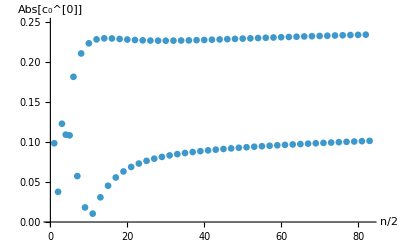

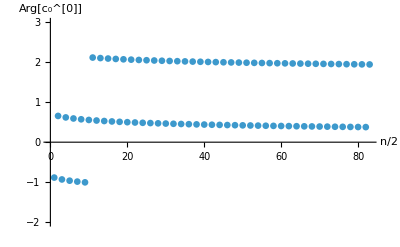

```mathematica
ps=0.012;
c00tabplotabs=ListPlot[Table[{n,c00tab[[n,1]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{0.0,0.25}},AxesLabel->{"n/2","Abs[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c00tabplotangle=ListPlot[Table[{n,c00tab[[n,2]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{-2,3}},AxesLabel->{"n/2","Arg[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

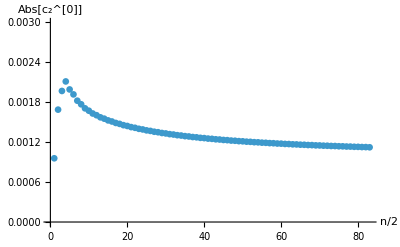

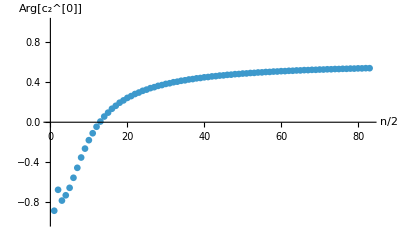

```mathematica
c20tabplotabs=ListPlot[Table[{n,c20tab[[n,1]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{0.0,0.003}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c20tabplotangle=ListPlot[Table[{n,c20tab[[n,2]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{-1,1}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

{param_0→0.247105,param_1→-0.636315,param_2→5.08432}

{param_0→0.115257,param_1→-0.638728,param_2→2.08655}

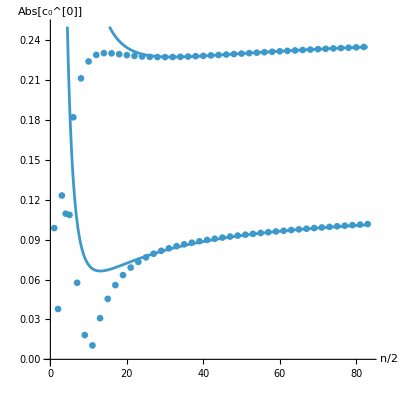

```mathematica
c00funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,1]]},{n,15,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot1=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.25}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,1]]},{n,15,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot2=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.25}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotabs,AxesLabel->{"n/2","Abs[c_0^[0]]"}]
```

```mathematica
(0.11525721412795355+0.24710457405685216)/16
```

0.0226476

```mathematica
0.022647611761550356
```

{param_0→0.286879,param_1→4.41213,param_2→-26.0647}

{param_0→1.85768,param_1→4.458,param_2→-26.096}

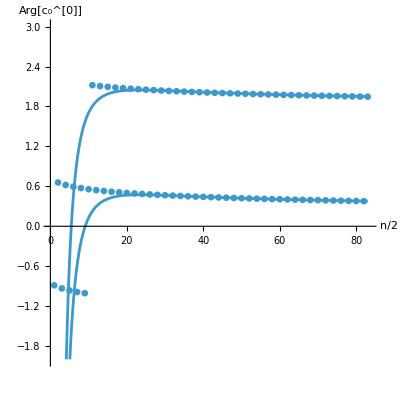

```mathematica
c00funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot1=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-2,3}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot2=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-2,3}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotangle,AxesLabel->{"n/2","Arg[c_0^[0]]"}]
```

{param_0→0.000983095,param_1→0.0127764,param_2→-0.0704633}

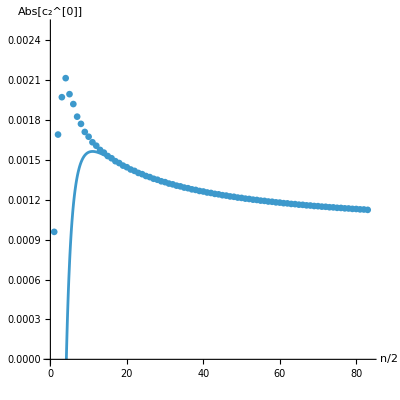

```mathematica
c20funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,1]]},{n,15,Length[c20tab]}],c00funabs,parameters,n]
fitplot=Plot[c20funabs/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{0.0,0.0025}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotabs]
```

{param_0→0.616578,param_1→-5.67419,param_2→-40.4897}

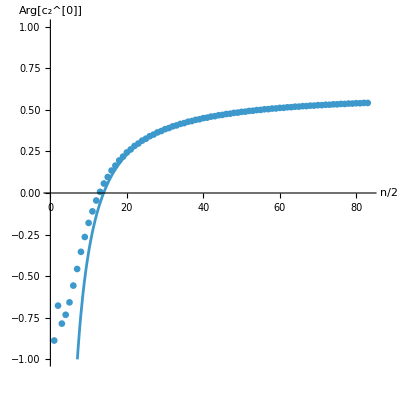

```mathematica
c20funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,2]]},{n,30,Length[c20tab]}],c00funangle,parameters,n]
fitplot=Plot[c20funangle/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{-1,1}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotangle]
```